```mathematica
A={{0,-1,1},{1,0,-1},{-1,1,0}};
```

```mathematica
MatrixForm[A]
```

(0 | -1 | 1
1 | 0 | -1
-1 | 1 | 0)

```mathematica
w={{x},{y},{1-x-y}};
```

```mathematica
MatrixForm[Expand[A.w]]
```

(1-x-2 y
-1+2 x+y
-x+y)

```mathematica
p1[x_,y_]:=1-x-2 y;p2[x_,y_]:=-1+2 x+y;
p3[x_,y_]:=-x+y;
```

```mathematica
Expand[Transpose[w].A.w]
```

{{0}}

```mathematica
p[x_,y_]:=0;
```

```mathematica
P[x_,y_]:=x(p1[x,y]-p[x,y]);Q[x_,y_]:=y(p2[x,y]-p[x,y]);
```

```mathematica
Solve[{P[x,y]==0&&Q[x,y]==0},{x,y}]
```

{{x→0,y→1},{x→1/3,y→1/3},{x→1,y→0},{x→0,y→0}}

```mathematica
Jac:=D[{P[x,y],Q[x,y]},{{x,y}}]
```

```mathematica
Jac/.{x->10/17,y->116/323}
```

{{-17/19,-20/17},{232/323,17/19}}

```mathematica
MatrixForm[%]
```

(-17/19 | -20/17
232/323 | 17/19)

```mathematica
Eigenvalues[%]
```

{(ⅈ √4639)/323,-(ⅈ √4639)/323}

```mathematica
N[%]
```

{0.+0.210868 ⅈ,0.-0.210868 ⅈ}

```mathematica
s=NDSolve[{x'[t]==P[x[t],y[t]],y'[t]==Q[x[t],y[t]],x[0]==.25,y[0]==.25},{x,y},{t,0,100}];
```

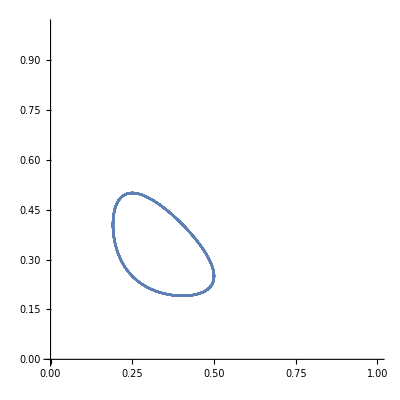

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.s],{t,0,100},PlotRange->{{0,1},{0,1}}]
```

```mathematica
Print[p1[.25,.25],"   ",p2[.25,.25],"   ",p3[.25,.25]]
```

0.25   -0.25   0.

```mathematica
{x[1],y[1]}/.s
```

{{0.326075,0.203895}}

```mathematica
Print[p1[.933,.056],"   ",p2[.933,.056],"   ",p3[.933,.056]]
```

-0.045   0.922   -0.877

```mathematica
{x[2],y[2]}/.s
```

{{0.414498,0.191209}}

```mathematica
Print[p1[.865,.135],"   ",p2[.865,.135],"   ",p3[.865,.135]]
```

-0.135   0.865   -0.73

```mathematica
{x[5.5],y[5.5]}/.s
```

{{0.417153,0.391499}}

```mathematica
Print[p1[.170,.796],"   ",p2[.170,.796],"   ",p3[.170,.796]]
```

-0.762   0.136   0.626